```mathematica
SetDirectory["D:\\Qsync\\QOLab\\Data\\On Resonance Project\\Lab Book 2 (18 Mar 29 -)\\20-09-28\\Power\\85F21"];
data=Import[#]&/@FileNames["*csv"];
data2=Table[Take[data[[i]],{17,-2}],{i,1,Length[data]}];
SetDirectory["D:\\Qsync\\QOLab\\Data\\On Resonance Project\\Lab Book 2 (18 Mar 29 -)\\20-09-28\\Power\\85F21\\Off"];
dataoff=Import[#]&/@FileNames["*csv"];
data2off=Table[Take[dataoff[[i]],{17,-2}],{i,1,Length[dataoff]}];
```

```mathematica
f[data_]:=Module[{ll,max,min,yaxis1,yaxis2,wcn,ff,gg,loc,kk},
ll=data[[All,2]];
{max,min}=#[ll]&/@{Max,Min};
yaxis1=Take[data[[All,4]],Flatten[{#[ll,min][[1]],#[ll,max][[-1]]}&@Position]];
yaxis2=Take[data[[All,8]],Flatten[{#[ll,min][[1]],#[ll,max][[-1]]}&@Position]];

wcn=(794.76728224*10^-9);


ff[x_]:=Evaluate[Fit[


Flatten[{Table[{o,yaxis1[[o]]},{o,10,200}],Table[{o,yaxis1[[o]]},{o,Length[yaxis1]-200,Length[yaxis1]-10}]},1]

,{1,x},x]];
gg=Table[ff[x],{x,1,Length[yaxis1]}];
loc=Select[FindPeaks[
GaussianFilter[yaxis2,10]
,16,0.00002],1500<#[[1]]<4500&];


kk[x_]:=Evaluate[Fit[{{loc[[1,1]],-0.361},{loc[[-1,1]],0}},{1,x},x]];
{-12.531885282826405 wcn Log[yaxis1/gg],GaussianFilter[yaxis1/gg,5],yaxis2,Table[kk[x],{x,1,Length[yaxis1]}]}

]
```

```mathematica
Manipulate[
ListPlot[{GaussianFilter[data2[[i]][[All,8]],10],
Select[FindPeaks[
GaussianFilter[data2[[i]][[All,8]],10]
,16,0.00002],1500<#[[1]]<4500&]},PlotStyle->{Black,{Red,AbsolutePointSize[5]}}]
,{{i,62},1,Length[data2],1}]
```

ListPlot::lpn: {{{1.,0.209159},{2.,0.209172},{3.,0.209178},{4.,0.209176},{5.,0.209189},{6.,0.209182},{7.,0.209174},{8.,0.209167},{9.,0.209162},{10.,0.20916},{11.,0.209184},{12.,0.209198},{13.,0.209238},{14.,0.209266},«23»,{38.,0.208992},{39.,0.208974},{40.,0.208964},{41.,0.208923},{42.,0.20892},{43.,0.208915},{44.,0.208915},{45.,0.208942},{46.,0.208978},{47.,0.20902},{48.,0.209049},{49.,0.209088},{50.,0.209137},«6200»},{}} is not a list of numbers or pairs of numbers.

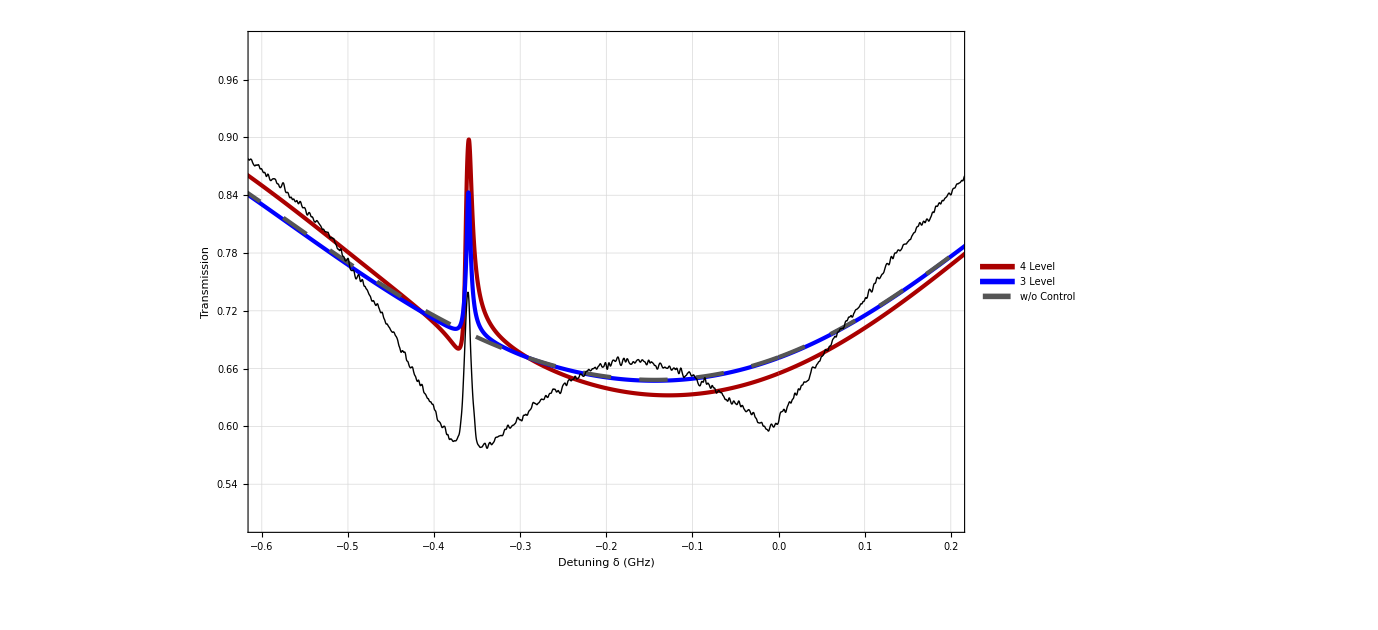

```mathematica
final2=ListPlot[{Lev4DoppTestsc[23,15/1000,0.9/1000,1.438*10^6,-361*10^6,0],Lev3DoppTestsc[23,15/1000,0.9/1000,1.438*10^6,-361*10^6,0],Lev3DoppTestsc[23,0/1000,1/1000,0.5*10^6,0*10^6,0]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Bottom}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Darker[Gray],Dashing[.02]},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning δ (GHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{{-0.6,0.2},{0.5,1.0}}];
Show[final2,ListPlot[Transpose[f[data2[[45]]][[{4,2}]]],Joined->True,PlotStyle->{Thick,Black},Epilog->Line[{{-2,1},{2,1}}]]]
```

```mathematica
Manipulate[ListPlot[Transpose[f[data2[[i]]][[{4,2}]]],PlotRange->{{-0.01-0.361,0.05-0.361},All},Joined->True,Epilog->Line[{{-2,1},{2,1}}]],{{i,2},1,Length[data2],1}]
```

```mathematica
Log[Min/@Partition[EITmin7721,4]]
```

{-0.943007,-0.507208,-0.522695,-0.524666,-0.538702,-0.547035,-0.543539,-0.550359,-0.561633,-0.556993,-0.55415,-0.567817,-0.592095,-0.592186,-0.606346,-0.616696,-0.626803,-0.631012,-0.632111,-0.635826,-0.631974}

```mathematica
Partition[EITmax7721,4]
```

{{0.67029,0.667698,0.675679,0.676211},{0.678308,0.679785,0.677827,0.687239},{0.687252,0.68019,0.690285,0.689},{0.690009,0.689978,0.692907,0.703394},{0.703666,0.705603,0.702764,0.703936},{0.709114,0.7113,0.715485,0.709972},{0.71455,0.72138,0.720045,0.729264},{0.722732,0.724903,0.719007,0.725706},{0.722642,0.728245,0.729586,0.729372},{0.730685,0.733981,0.735279,0.733269},{0.735034,0.730526,0.73818,0.736487},{0.739317,0.739342,0.73697,0.749794},{0.749317,0.749324,0.75187,0.757763},{0.759913,0.758727,0.76186,0.757274},{0.762958,0.760504,0.762355,0.751314},{0.76157,0.767309,0.762804,0.76601},{0.762096,0.768288,0.764541,0.765574},{0.766139,0.768591,0.767195,0.768085},{0.769846,0.776804,0.770664,0.771582},{0.771688,0.765874,0.770202,0.771254},{0.76503,0.767294,0.769025,0.765602}}

```mathematica
Partition[EITmin7721,4]
```

```mathematica
EITmax7721L=Log[Mean/@{{0.6702904135692237,0.6676982095218721,0.6756793577110468,0.676211482452694},{0.6783083009292048,0.6797850505426076,0.677826799220555,0.6872392503553362},{0.687252304246403,0.6801899526215857,0.6902846390051267,0.6889999049727629},{0.6900091276401121,0.6899780822408025,0.6929071267391882,0.7033935481341589},{0.7036664260805991,0.7056026304767509,0.7027643732887916,0.7039359237693468},{0.7091144867774567,0.7112999756651736,0.7154852809033403,0.7099716890212582},{0.7145495082917785,0.7213798133393889,0.7200447054366548,0.7292639204331729},{0.7227319880297841,0.7249028842290456,0.7190073642860041,0.7257059728277393},{0.7226424752026791,0.7282447269161065,0.7295859355315983,0.7293723403793567},{0.7306853984862662,0.7339805195475569,0.7352788293999454,0.7332687971367688},{0.735033831634552,0.7305257165022221,0.7381803368284257,0.7364872490513605},{0.7393165440015412,0.7393415837356018,0.7369704541533667,0.7497944107389106},{0.749316951401969,0.7493236655897443,0.7518701951288002,0.7577628475529251},{0.7599132444543931,0.7587265118052277,0.761859565425088,0.7572739808060635},{0.762958071620532,0.7605037903813792,0.7623553621526086,0.7513140621892629},{0.7615701804937012,0.7673086884326347,0.762803573765666,0.7660101989980699},{0.762096462384274,0.7682881310395208,0.7645413834485655,0.7655744379030776},{0.7661390402247394,0.7685908274603388,0.7671948818953783,0.7680854318424767},{0.7698462350408909,0.7768040034922258,0.7706636203960422,0.7715820746026785},{0.7716883670662569,0.7658735769906674,0.7702021685627674,0.7712538562880025},{0.7650299010742044,0.7672941029306063,0.7690249923235025,0.7656020818383771}}]
```

{-0.396798,-0.384502,-0.375884,-0.36518,-0.350988,-0.340425,-0.326687,-0.324226,-0.318194,-0.310196,-0.307808,-0.299275,-0.284928,-0.27517,-0.275381,-0.268634,-0.267716,-0.264613,-0.258481,-0.261684,-0.26561}

```mathematica
EITmin7721L=Log[Mean/@{{0.6148507237800379,0.6148507237800379,0.6148507237800379,0.6148507237800379},{0.61301814540491,0.6141956305453045,0.6139257874881182,0.602174593252282},{0.6053495855589126,0.5996390850268525,0.6069015720599724,0.592920299485528},{0.5948836314206307,0.5969434600450824,0.5917528025989898,0.5933337241926111},{0.5901574869349875,0.5930827257080711,0.593183817277664,0.583505144925634},{0.5845970639283866,0.5879850885173781,0.5857045253948573,0.5786632120272109},{0.5806896630734512,0.5848963809543001,0.58373580537662,0.581783273275648},{0.5809463437284291,0.5810699054797882,0.57830425939723,0.5767424527482139},{0.5770580356672879,0.5784311346349769,0.5761430555686995,0.5702768871239002},{0.5729291544285126,0.576659499309907,0.5774154377339757,0.5781207429393022},{0.5755058458237288,0.5760714357596861,0.5745601441672286,0.5750364228401794},{0.5772744346684539,0.5759740335459484,0.5737076745814482,0.566761399348981},{0.5641571990309093,0.5649601182176355,0.5660739316859412,0.5531671582241214},{0.555792194173992,0.5531168037334115,0.5531541697250305,0.5543512780069711},{0.5484970530738279,0.5453399835681709,0.5509863730019976,0.5459634132062252},{0.5397245862264335,0.5423468720890051,0.540006747329948,0.5410321043298213},{0.5342972456508458,0.5364267265288724,0.537111929885265,0.5357730404458924},{0.5381698903669229,0.5353067111645343,0.5320529288683835,0.5342022405459145},{0.5342918595115004,0.5346212638736029,0.532499279031823,0.5314688460562479},{0.5409252063427161,0.533021198837631,0.5294978882510722,0.5330503324415664},{0.5315415861442944,0.5355131940251052,0.5326928986850257,0.5342132517910168}}]
```

{-0.486376,-0.492939,-0.508823,-0.520492,-0.527663,-0.537448,-0.539952,-0.545994,-0.552556,-0.55116,-0.552875,-0.55612,-0.576094,-0.590404,-0.602034,-0.614747,-0.623804,-0.625614,-0.628821,-0.627128,-0.628315}

```mathematica
EITmax7721=Table[
If[i<47,
Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.01-0.361<#[[1]]<0.025-0.361&][[All,2]]//Max,
Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.01-0.361<#[[1]]<0.05-0.361&][[All,2]]//Max],{i,1,Length[data],1}];
```

```mathematica
EITmin7721=Table[
If[i<47,
Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.01-0.361<#[[1]]<0.05-0.361&][[All,2]]//Min,
Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.01-0.361<#[[1]]<0.05-0.361&][[All,2]]//Min],{i,1,Length[data],1}];
```

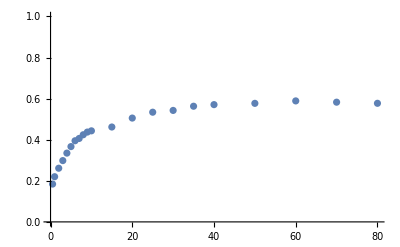

```mathematica
rb8521=ListPlot[{Transpose[{pw,1-EITmax7721L/EITmin7721L}]},PlotRange->{0,1}]
```

```mathematica
Table[Select[Transpose[f[data2off[[1]]][[{4,2}]]],-0.02<#[[1]]<0.02&][[All,2]]//Min,{i,1,Length[dataoff],1}]//Mean
```

0.546944

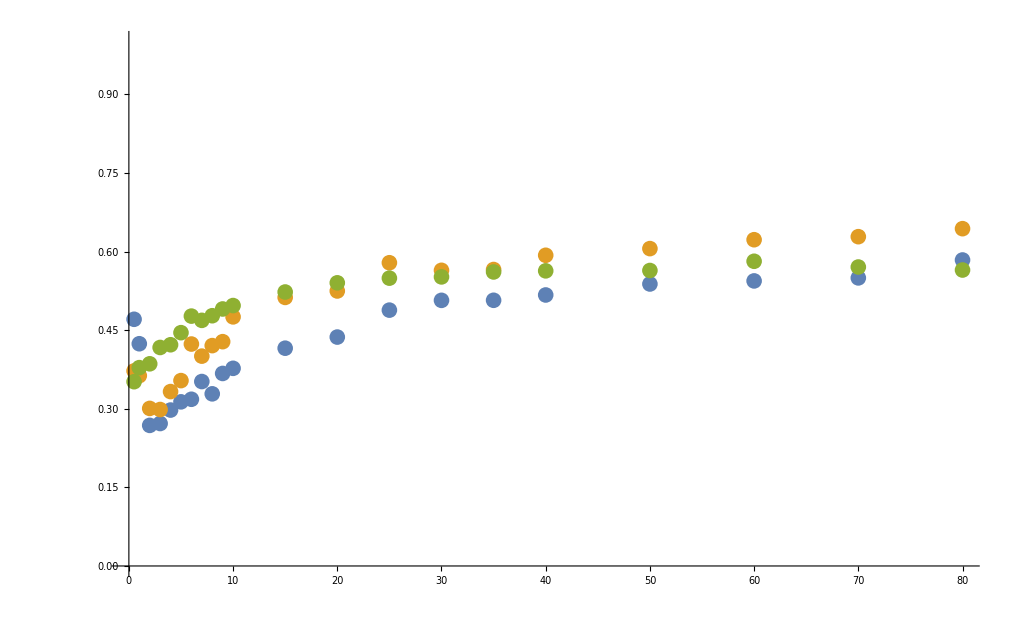

ListPlot::lpn: {{{1.,0.209159},{2.,0.209172},{3.,0.209178},{4.,0.209176},{5.,0.209189},{6.,0.209182},{7.,0.209174},{8.,0.209167},{9.,0.209162},{10.,0.20916},{11.,0.209184},{12.,0.209198},{13.,0.209238},{14.,0.209266},«23»,{38.,0.208992},{39.,0.208974},{40.,0.208964},{41.,0.208923},{42.,0.20892},{43.,0.208915},{44.,0.208915},{45.,0.208942},{46.,0.208978},{47.,0.20902},{48.,0.209049},{49.,0.209088},{50.,0.209137},«6200»},{}} is not a list of numbers or pairs of numbers.

```mathematica
ListPlot[{Transpose[{pw,1-Log[Max/@Partition[EITmax7711,4]]/Log[0.48]}],Transpose[{pw,1-Log[Max/@Partition[EITmax7712,4]]/Log[0.7635754329884742]}],Transpose[{pw,1-Log[Max/@Partition[EITmax7721,4]]/Log[0.5469]}]},PlotRange->{0,1},ImageSize->1020,PlotRange->{0,0.8}]
```